# The Magnitude of the Correlation Coefficient

## Theme

```mathematica
fontLabels=Directive[FontFamily->"Libertinus Serif",FontSize->22];
fontTicks=Directive[FontFamily->"Libertinus Serif",FontSize->18];

(* https://mathematica.stackexchange.com/questions/54545/is-it-possible-to-define-a-new-plottheme *)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)

resolvePlotTheme["myThemeBasic",def:_String]:=Themes`SetWeight[
Join[
{ImageSize->Large},
{LabelStyle->fontLabels},
{TicksStyle->fontTicks},
{FrameTicksStyle->fontTicks},
(* 102 is the default grey level of Mathematica *)
{AxesStyle->Directive[AbsoluteThickness[0.3],GrayLevel[102/255]]}
]
,$ComponentWeight];
resolvePlotTheme["myTheme",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Directive[PointSize[0.013],Thick]}
]
,$ComponentWeight];
resolvePlotTheme["myThemeBW",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myTheme",def],
{PlotStyle->Thread@Directive[{GrayLevel[0.2],GrayLevel[0.8]},Thick,{Automatic,Dashed}]}
]
,$ComponentWeight];
(* Do not adjust point sizes for region plots *)
resolvePlotTheme["myTheme",def:"RegionPlot"]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Automatic}
]
,$ComponentWeight];

End[];

it[var_]:=Style[var,FontSlant->Italic]
bf[var_]:=Style[var,FontWeight->Bold]
bi[var_]:=bf[it[var]]
```

## Part 1: Noise Influence

Increase of σ_y: r_XY decreases but the linear relationship is still present

Increase of σ_x: same as for σ_y, only in the x-direction

Increase both: this decreases r_XY even more but the linear relationship is not present anymore. Only Gaussian noise is visible

## Part 2:

The underlying cause here is how the regression line is calculated: it measures the difference between the points and the corresponding y-intercept on the line, i.e. the dependency from X (independent variable) to Y (dependent variable).

When we increase σ_x, the points scatter around more to the right and left which leads to a new fit for the regression line.

When we increase σ_y, the points scatter mainly up and down. This does only increase the distance to the y-intercept but the regression line itself stays roughly the same.

If we changed the plot axes, the effects would reverse.

## Code

```mathematica
(* https://mathematica.stackexchange.com/questions/54545/is-it-possible-to-define-a-new-plottheme *)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)

resolvePlotTheme["myTheme",def:_String]:=
Themes`SetWeight[Join[
{ImageSize->Large},
{LabelStyle->Directive[FontFamily->"Libertinus Serif",FontSize->20]},
{TicksStyle->Directive[FontSize->16]}
]
,$ComponentWeight];

End[];
```

```mathematica
SeedRandom[1337];
```

```mathematica
deviationBar[y0_,μ_,σ_,reverse_?BooleanQ,scale_]:=Block[{midBar,textStyle,lineStyle,rev},
midBar=scale;
textStyle=CurrentValue[{StyleDefinitions,"GraphicsLabel"}];
rev=Piecewise[{{Reverse, reverse}, {Identity, True}}];

Graphics[{
{
RGBColor[0.880722, 0.611041, 0.142051],
Thickness[Absolute[1.6]],
Line[{rev[{μ-σ,+y0}],rev[{μ+σ,+y0}]}],
Line[{rev[{μ,midBar+y0}],rev[{μ,-midBar+y0}]}],
Line[{rev[{μ-σ,midBar+y0}],rev[{μ-σ,-midBar+y0}]}],
Line[{rev[{μ+σ,midBar+y0}],rev[{μ+σ,-midBar+y0}]}]
},

Text[Style["μ",FontFamily->"Libertinus Serif",FontSize->16,textStyle],rev[{μ,-2.3*midBar+y0}]],
Text[Style["-σ",FontFamily->"Libertinus Serif",FontSize->16,textStyle],rev[{μ-0.5*σ,-2.3*midBar+y0}]],
Text[Style["+σ",FontFamily->"Libertinus Serif",FontSize->16,textStyle],rev[{μ+0.5*σ,-2.3*midBar+y0}]]
}]
]

plotLine[σx_,σy_]:=Module[{xValues,yValues,lm,data},
xValues=Range[-4,4,0.001];
yValues=xValues*2;

(* Add noise *)
xValues=xValues+RandomVariate[NormalDistribution[0,σx],Length[xValues]];
yValues=yValues+RandomVariate[NormalDistribution[0,σy],Length[yValues]];

data={xValues,yValues}ᵀ;
lm=LinearModelFit[{xValues,yValues}ᵀ,x,x];

Show[
ListPlot[data,
PlotTheme->"myTheme",
PlotLegends->{"(x_i, y_i)"},
PlotRange->{{-20,20},{-40,40}},
AspectRatio->1,
AxesLabel->{x,y},
PlotStyle->Opacity[0.5],
PlotLabel->Column[{
Row[{"r_XY = ",Correlation[data][[1,2]]}],
Row[{"{s_X, s_Y} = ",StandardDeviation[data]}],
Row[{"s_XY = ",Covariance[data][[1,2]]}]
}]
],
Plot[lm[x],{x,-20,20},PlotTheme->"myTheme",PlotStyle->RGBColor[0.915, 0.3325, 0.2125],PlotLegends->{"Trend"}],

deviationBar[-45,Mean[data][[1]],StandardDeviation[data][[1]],False,1.4]/.{"μ"->"x̄","-σ"->"-s_X","+σ"->"+s_X"},
deviationBar[-22,Mean[data][[2]],StandardDeviation[data][[2]],True,0.8]/.{"μ"->"ȳ","-σ"->"-s_Y","+σ"->"+s_Y"},

ImagePadding->{{60,Automatic},{60,Automatic}},
PlotRangeClipping->False,
ImageSize->Large
]
]
```

```mathematica
σxMin=0.1;
σxMax=4.9;
σxStep=0.2;
σyMin=0.1;
σyMax=9.7;
σyStep=0.4;

Manipulate[
plotLine[σx,σy]
,{{σx,σxMin,"σ_X"},σxMin,σxMax},{{σy,σyMin,"σ_Y"},σyMin,σyMax}]
```

```mathematica
(*Do[
Export[
FileNameJoin[{
NotebookDirectory[],
"frames/sigmaX="<>IntegerString[Round[(σx-σxMin)/σxStep,1],10,2]<>"sigmaY=00.png"
}],
Flatten[Table[plotLine[σx,σy],{σy,σyMin,σyMax,σyStep}],1],
"VideoFrames",
Antialiasing->True
];

,{σx,σxMin,σxMax,σxStep}
]*)
```

```mathematica
data2={RandomVariate[NormalDistribution[],10000],RandomVariate[NormalDistribution[0,5],10000]}ᵀ;
```

```mathematica
data2=data2.RotationMatrix[10°];
```

```mathematica
lm2=LinearModelFit[data2,x,x];
```

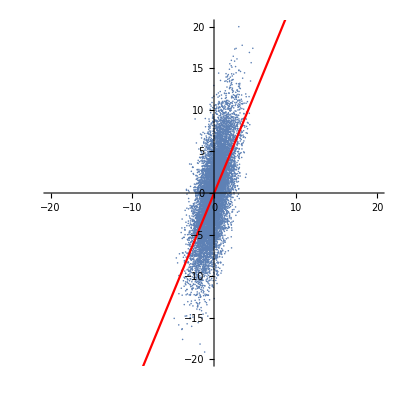

```mathematica
Show[
ListPlot[data2,AspectRatio->1,PlotRange->{{-20,20},{-20,20}}],
Plot[lm2[x],{x,-20,20},PlotStyle->Red]
]
```